# Sphere packing bounds for d = 100

```mathematica
(* This Notebook computes the Linear programming (LP) bound on packing density of spheres in Euclidean space in d=100 dimensions. d=100 is chosen as a sample dimension. For d=100, it takes about half an hour to run the notebook. One should be able to run the notebook all the way to additional material section which are about other dimensions that I have included but didn't run it in the notebook.

 I wrote the code and used a similar notebook to compute the linear programming bound in high dimensions d~4096 in Cornell's computer cluster which is the record known upper LP bound on sphere packing. For more details, see https://arxiv.org/pdf/2006.02560.pdf. There are two very interesting cases corresponding to d=8, 24 where LP bounds gives answers that are really close to integers. I added the case d=24 result as additional material which corresponds to optimal packing on the Leech lattice. Please have a look at the d=24 section to see how close the coefficients are to Leech lattice. It takes about 15 mins to generate high precision data for the Leech lattice 
The mathematical formulation of the notebook is the following: Given N, solve Subscript[f, k](0) + ∑_(n=1)^N Subscript[d, n] Subscript[f, k](Subscript[Δ, n]) = 0 for 1≤ k ≤ 2N, where Subscript[d, 1],...,Subscript[d, N] and Subscript[Δ, 1],..., Subscript[Δ, N] are 2N unknowns in the problem. Subscript[f, j](Δ) is defined as Subscript[f, j](Δ) = Subscript[L^(d/2-1), 2j-1] (4π Δ) ⅇ^(-2πΔ) ,where Subscript[L^(d/2-1), k] is the Laguerre polynomial. After solving these 2N equations for 2N variables, Subscript[Δ, 1] gives the bound on packing density. Higher N means more number of equations and therefore it requires higher computational power. For a given hyperparameter like the dimension of the euclidean space d, N should be roughtly N~ d so to make sure the bounds have converged. *)
```

### HyperParameters

```mathematica
(* d is the Euclidean space dimension, cent =d/2 which is the central charge in the CFT formulation, N1 is the related to symmetry algebra characters of modules which are 
U(1)^(2cent) in the sphere packing problem *)
d=100;
cent=d/2;
N1=cent;
(* precision is the number of digits I kept for each number. For the matrix inversion when and element is smaller than cutoff, I substitute it with 0, stoppingThreshold is when we stop Newton's method *)

myprec= 400;
cutoff= 10^-myprec;
precise[x_]:= SetPrecision[x,myprec];
stoppingThreshold=10^-10;
```

## Functions

```mathematica
(* vander  is computing vANDERMONT IN THE NOTE, ROWS ARE Subscript[P, i](Subscript[r, j]) (P`)_i(rj), it's a square matrix, much faster than computing Laguerre polynomials with mathematica *)
```

```mathematica
vander[X_]:=Module[{row,drow},
row[0]=Table[1,{Length[X]}];
row[1]=Table[1-2 precise[x],{x,X}];
drow[1]=Table[-2,{Length[X]}];
res1=Table[row[i]=(SS1[i] row[i-2]+SS2[i,X]*row[i-1])//precise;
drow[i]=(drow[i-1]-2 row[i-1])//precise;
Join[(row[i][[1;; Length[X] ]]),(drow[i][[1;;Length[X] ]]) ]//precise,{i,2,4 Length[X]-1}];
Join[{Join[row[1][[1;;Length[X]]],drow[1][[1;;Length[X]]] ]},res1]//precise];
```

```mathematica
(*coeff is computing coefficients Subscript[d, i]'s after multiplying by exponentioal factor and vacuum, for an example see J function *)
coeff[v0_, list_]:= Module[{n,colum,max,cs,rs,seed,lag,mat, one,vaclis,vc,row},
n=Length[list]/2;
rs=list[[1;;n]];
cs=list[[n+1;;2n]];


vaclis={v0,v0+2  π, v0+4 π}//precise;
vc[0]=Table[1,{i,3}];
vc[1]= 5-2 vaclis;
Table[vc[i]=1/i(-(3+i)* vc[i-2]+(2 i-1-2 vaclis+4)*vc[i-1])//precise; vc[i] ,{i,2,2 (2n)-1}];

row[0]=Table[1,{Length@rs}];
row[1]=5-2 rs;
seed=Table[ row[i]  =1/i ((1-i)* row[i-2]+(2i-1- 2 rs)*row[i-1])//precise; row[i],{i,1,2 (2n)-1}];
colum=Transpose[Table[(vc[i][[1]]- 2  ⅇ^(-2π)vc[i][[2]]+ ⅇ^(-4π)vc[i][[3]])^-1 row[i]//precise
,{i,1,2(2n)-1,2}]];
mat= Table[ MaximalBy[colum[[i]],Abs][[1]]//precise,{i,Length@colum}];
ClearSystemCache[];
Table[(cs[[i]]/mat[[i]] ⅇ^(rs[[i]]-v0))//precise,{i,1,n}]

]/;VectorQ[list,NumericQ]
```

```mathematica
(*this is objective (loss) function. When it is zero, the solutions are found. *)
```

```mathematica
obj[v0_, list_]:= Block[{n,colum,max,cs,rs,seed,lag,mat, one,vaclis,vc,row},
n=Length[list]/2;
rs=list[[1;;n]];
cs=list[[n+1;;2n]];
one= Table[1,{i,1,2n}];



vaclis={v0,v0+2  π, v0+4 π}//precise;
vc[0]=Table[1,{i,3}];
vc[1]= (N1-2 vaclis)//precise;
Table[vc[i]=1/i(-(N1-2+i)* vc[i-2]+(2 i-1-2 vaclis+N1-1)*vc[i-1])//precise; vc[i] ,{i,2,2 (2n)-1}];




row[0]=Table[1,{Length@rs}];
row[1]=N1-2 rs//precise;
seed={row[1]//precise}~Join~Table[ row[i]  =1/i (-(N1-1-1+i)* row[i-2]+(2i-1- 2 rs+N1-1)*row[i-1])//precise; row[i],{i,2,2 (2n)-1}];
colum=Transpose[Table[(vc[i][[1]])^-1 row[i]//precise,{i,1,2(2n)-1,2}]];
mat= Table[ colum[[i]]/(MaximalBy[colum[[i]],Abs][[1]])//precise,{i,Length@colum}];

result=cs.mat +one;
lastR=list;
lastErr = result.result;
ClearSystemCache[];
result
]/;VectorQ[list,NumericQ]


(* J is computing Jacobian of loss function  *)
```

```mathematica
J[v0_,list_]:= Block[{a={},colum, max,mat,dmat,seed,dseed,rs, lag,cs,c,leng,c0,r,r0,k,n,t,o={},j,i,vaclis,kkk,vc,row,drow},
leng=Length[list];
n=leng/2;
r0=list[[1]];
c0= list[[n+1]];
rs= list[[1;;n]];
cs= list[[n+1;;2n]];

vaclis={v0,v0+2  π, v0+4 π}//precise;
vc[0]=Table[1,{i,3}];
vc[1]= (N1-2 vaclis)//precise;
Table[vc[i]=1/i(-(N1-2+i)* vc[i-2]+(2 i-1-2 vaclis+N1-1)*vc[i-1])//precise; vc[i] ,{i,2,2 (2n)-1}];


row[0]=Table[1,{Length@rs}];
row[1]=(N1-1+1-2 rs)//precise;
drow[1]=Table[-2,{Length@rs}];
Table[ row[i]  =1/i (-(N1-1-1+i)* row[i-2]+(2i-1- 2 rs+N1-1)*row[i-1])//precise; row[i],{i,2,2 (2n)-1}];
Table[drow[i]=1/(i-1)((i-1-2 rs) drow[i-1] - 2 (i-1+N1-1)row[i-2])//precise;drow[i],{i,2,2 (2n)-1}];

seed=Transpose[Table[(vc[i][[1]])^-1 row[i]//precise,{i,1,2(2n)-1,2}]];
dseed=Transpose[ Table[(vc[i][[1]])^-1 drow[i]//precise,{i,1,2(2n)-1,2}]];
mat= Table[max[i]=MaximalBy[seed[[i]], Abs][[1]]; k[i]=(Position[seed[[i]],max[i]]//Flatten)[[1]];seed[[i]]/max[i],{i, Length@seed}];
dmat=  Table[dseed[[i]]/max[i]- (seed[[i]]* dseed[[i,k[i]]])/(max[i])^2//precise,{i, Length@dseed}];

ClearSystemCache[];
Transpose[Join[cs* dmat,mat]]
 ]/;VectorQ[list,NumericQ]
```

```mathematica
(*smartguess is the guessing the next asnwer based on only previous one by rescaling*)
smartGuess[oldroots_,oldN_,newN_]:=Module[{rRef,res,i},rRef=ListInterpolation[oldroots];
rNew[i_]:=(oldroots[[1]] (1-newN/oldN)+newN/oldN rRef[1+(i-1)*(oldN-2)/(newN-2)])//precise;
res=Table[rNew[i],{i,newN/2}]];


(*smartguess 2  is guessing a better answer by considering the difference between solutions and guesses and make a better guess*) 
smartGuess2[diffold1_,diffold2_,oldN1_,oldN2_,newN_]:=Module[{rRef1,rRef2,res,i},rRef1=ListInterpolation[diffold1];rRef2= ListInterpolation[diffold2];
rNew[i_]:=((newN/oldN2)rRef2[1+(i-1)*((oldN2-2)/(newN-2))]+(newN-oldN2)(1/(oldN2-oldN1)(rRef2[1+(i-1)*((oldN2-2)/(newN-2))] -rRef1[1+(i-1)*((oldN1-2)/(newN-2))] )))//precise;
res=Table[rNew[i],{i,newN/2}]];
```

```mathematica
(*A better guess is based on fitting multiple plots to log functions and finding an even better guess compared to smartguess2. The error for this guess is 10^-3 for typical jump whereas smartguess2 has 10^-2 error. Using trials and errors, different interpolationorder and combination of powers of logs sometimes give better guess *) 
Clear[rfitguess]
nlguess[reclist_,nnew_]:=Module[{},rfitguess={};
For[curi=1,curi≤nnew/2,curi++,rofn=Table[{reclist[[indexn]],Interpolation[rootsave[reclist[[indexn]]],InterpolationOrder->15][curi*reclist[[indexn]]/nnew]},{indexn,1,Length@reclist}]//Quiet;
fitrofn=Fit[rofn,{1,ni}~Join~Table[Log[ni]^i,{i,1,3,1}],ni];
AppendTo[rfitguess,fitrofn/.ni->nnew];];
rfitguess//precise]
nlguess2[reclist_,nnew_]:=Module[{},rfitguess={};
For[curi=1,curi≤nnew/2,curi++,rofn=Table[{reclist[[indexn]],Interpolation[rootsave[cent,reclist[[indexn]]],InterpolationOrder->13][curi*reclist[[indexn]]/nnew]},{indexn,1,Length@reclist}]//Quiet;
fitrofn=Fit[rofn,{1,ni}~Join~Table[Log[ni]^i,{i,1,3,1}],ni];
AppendTo[rfitguess,fitrofn/.ni->nnew];];
rfitguess//precise]
nlguess3[reclist_,nnew_]:=Module[{},rfitguess={};
For[curi=1,curi≤nnew/2,curi++,rofn=Table[{reclist[[indexn]],Interpolation[rootsave[cent,reclist[[indexn]],nn2],InterpolationOrder->13][curi*reclist[[indexn]]/nnew]},{indexn,1,Length@reclist}]//Quiet;
fitrofn=Fit[rofn,{1,ni}~Join~Table[Log[ni]^i,{i,1,3,1}],ni];
AppendTo[rfitguess,fitrofn/.ni->nnew];];
rfitguess//precise]
hnlguess2[reclist_,nnew_]:=Module[{},rfitguess={};
For[curi=1,curi≤nnew/2,curi++,rofn=Table[{reclist[[indexn]],Interpolation[rootsave[cent,reclist[[indexn]]],InterpolationOrder->13][curi*reclist[[indexn]]/nnew]},{indexn,1,Length@reclist}]//Quiet;
fitrofn=Fit[rofn,{1,ni}~Join~Table[Log[ni]^i,{i,1,5,1}],ni];
AppendTo[rfitguess,fitrofn/.ni->nnew];];
rfitguess//precise]

(*alpha is comuting the functional *)
Clear[αl]
αl[list_]:= Module[{N1,VhatT={}, v={},V,αlis,par},

N1= 2Length[list];
V=Drop[Take[vander6[list],{1,-1,2},All],None,{N1/2+1,N1/2+1}];
v=Take[V,-1,All]//Flatten;
VhatT=Transpose[ Drop[V,-1,None]];
αlis=- LinearSolve[VhatT,v,Method-> Automatic];
αlis~Join~{1}

(*((αlis~Join~{1}).V)[[1]]*)
]
Clear[poly]
poly[list_]:= Module[{N1,VhatT={}, v={},V,αlis,par},

N1= 2Length[list];
V=Drop[Take[vander6[list],{1,-1,2},All],None,{N1/2+1,N1/2+1}];
v=Take[V,-1,All]//Flatten;
VhatT=Transpose[ Drop[V,-1,None]];
αlis=- LinearSolve[VhatT,v,Method-> Automatic];
Sum[(αlis~Join~{1})[[i]] LaguerreL[2i-1,2x],{i,1,N1}]

(*((αlis~Join~{1}).V)[[1]]*)
]
(*fT is final loss function, Df is the final Jacobian *)

fT[Xint_]:= obj[-2π(cent-N1)/12, Xint];
Df[X_]:= J[-2π(cent-N1)/12 ,X];

(* stepOK checks whether the differences between roots are reasonable or not *)
stepOK[X_]:=Module[{},vR=X[[1;;Length[X]/2]];
vC=X[[Length[X]/2+1;;]];
Min[Differences[vR]]>precise[2 π*0.5]];
```

```mathematica
(*Newtons's method, many elements of jacobian matrix are small. setting the ones below a cutoff to zero makes the inversion of matrix much faster *)
```

```mathematica
Clear[newtonMinimizer,newtonMinimizer2]
rootN={};
```

```mathematica
stoppingThreshold=10^-6;
newtonMinimizer2[Xinit_]:=Module[{},ll={};cc={};nmtick=AbsoluteTime[];
Nv=Length[Xinit];
f0=fT[Xinit];
X=Xinit;
continue=True;
itercount=0;
While[continue,jac=Chop[Df[X],cutoff];
(*Jinv=Inverse[jac,Method->Automatic];
dX=-Jinv.f0;*)
dX= -LinearSolve[jac,f0,Method->Automatic];
μ=1;
nX=X+μ dX;
(*if full newton step is unreasonable,take a shorter and shorter step*)While[μ>10^-15&&Not[stepOK[nX]],μ=μ/10;
nX=X+μ dX];
X=nX;

f0=fT[X];
ll=AppendTo[ll,f0.f0];

cc=AppendTo[cc, X[[Length[X]/2+1;; Length[X]]]];
If[f0.f0<stoppingThreshold,continue=False;
stopReason="success";];
itercount++;
If[itercount≥5000,continue=False;
stopReason="maxiters";
Print["ERROR: Exceeded maxiters"];];
If[μ<10^-12,continue=False;
stopReason="minstepsize";
Print["ERROR: Reached minstepsize"];];];
nmtime=AbsoluteTime[]-nmtick;
(*print results and return last X*)Print["N = ",Nv,"; err= ",lastErr//N,"; iters= ",itercount,"; newton time =",nmtime];
rootN=AppendTo[rootN,X[[1;; Length[X]/2]]];
X];
```

```mathematica
newtonMinimizer3[Xinit_]:=Module[{},ll={};cc={};nmtick=AbsoluteTime[];
Nv=Length[Xinit];
f0=fT[Xinit];
X=Xinit;
continue=True;
itercount=0;
μ=1;
While[continue,jac=Chop[Df[X],cutoff];
(*Jinv=Inverse[jac,Method->Automatic];
dX=-Jinv.f0;*)
dX= -LinearSolve[jac,f0,Method->Automatic];
nX=X+μ dX;
(*if full newton step is unreasonable,take a shorter and shorter step*)While[μ>10^-15&&Not[stepOK[nX]],μ=μ/10;
nX=X+μ dX];
X=nX;

f0=fT[X];
ll=AppendTo[ll,f0.f0];

cc=AppendTo[cc, X[[Length[X]/2+1;; Length[X]]]];
If[f0.f0<stoppingThreshold,continue=False;
stopReason="success";];
itercount++;
If[itercount≥5000,continue=False;
stopReason="maxiters";
Print["ERROR: Exceeded maxiters"];];
If[μ<10^-12,continue=False;
stopReason="minstepsize";
Print["ERROR: Reached minstepsize"];];];
nmtime=AbsoluteTime[]-nmtick;
(*print results and return last X*)Print["N = ",Nv,"; err= ",lastErr//N,"; iters= ",itercount,"; newton time =",nmtime];
rootN=AppendTo[rootN,X[[1;; Length[X]/2]]];
X];
```

```mathematica
(*Broyden method. it didn't work as well as Newton's method *)
```

```mathematica
Broyden1[Xinit_]:=Module[{},ll={};cc={};nmtick=AbsoluteTime[];
Nv=Length[Xinit];
f0=fT[Xinit];
X=Xinit;
continue=True;
itercount=0;
jac=Df[X];
(* H is inverse of Jac *)
H=-Inverse[jac,Method->Automatic];
While[continue,
f0=fT[X];
dX=H.f0;
μ=1;

cc=AppendTo[cc, X[[Length[X]/2+1;; Length[X]]]];
nX=X+μ dX;
(*if full newton step is unreasonabl
 

e,take a shorter and shorter step*)While[μ>10^-8&&Not[stepOK[nX]],μ=μ/10;
nX=X+μ dX];
df=fT[nX]-f0;
X=nX;
H= H- Outer[Times,(dX+ H.df)/(df.Transpose[H].dX),Transpose[H].dX];
ll=AppendTo[ll,f0.f0];

If[f0.f0<stoppingThreshold,continue=False;
stopReason="success";];

itercount++;
If[itercount≥1000,continue=False;
stopReason="maxiters";
Print["ERROR: Exceeded maxiters"];];
If[μ<10^-10,continue=False;
stopReason="minstepsize";
Print["ERROR: Reached minstepsize"];];];
nmtime=AbsoluteTime[]-nmtick;
(*print results and return last X*)Print["N = ",Nv,"; err= ",lastErr,"; iters= ",itercount,"; Broyden1 =",nmtime];
rootB=AppendTo[rootB,X[[1;; Length[X]/2]]];
X];
```

```mathematica
(*Gradient descent method. It was too slow *)
```

```mathematica
graDes[Xint_]:= Module[{},ll={};
nmtick=AbsoluteTime[];
β=0.8;
α=0.1;
X=Xint;
Nv= Length[Xint];
f0=ff[X];
continue=True;
itercount=0;
While[continue, 


t=1;
iter2=0;
While[ ff[ X- t Dff[X]]> ff[X]- α t Dff[X].Dff[X],
t= β t;
iter2++;
];
X= X-t Dff[X];
f0= ff[X];
itercount++;
AppendTo[ll,f0];

If[ f0<stoppingThreshold,continue=False;
stopReason="success";];

If[itercount≥10000,continue=False;
stopReason="maxiters";
Print["ERROR: Exceeded maxiters"];];

];
nmtime=AbsoluteTime[]-nmtick;
Print["N=",Nv," ; err=", f0, " ; iter= ",itercount," ; gradtime= ", nmtime]
]
```

## Computing Linear programming bounds to high precision

```mathematica
(*General strategy: 
Solving the equation at optimum corresponds to solving N non linear equation for N/2 location of roots and N/2 coefficients for each root. Due to non-convex nature of the problem, we need a good starting point for variables. The coefficients are appearing linearly and therefore, having a good guess is not necessary for them (although they have self-similar pattern as well). The equations are extremely sensitive to having a good guess for roots. We used previous optimized solution to guess a much larger solution. When we have small data, our jumps has to be small. For larger problems we predict the roots based on previous ones *)
```

```mathematica
(* first few roots, can be solved by interpolating previous results, or by playing with the starting point *)
mm=7;
FindRoot[fT[{r1,r2,r3,c1,c2,c3}], {r1,2π(mm)},{r2,(2π)(mm+2)},{r3, (2π )(mm+4)},{c1,-1},{c2,-1},{c3,-1},PrecisionGoal->100,AccuracyGoal->Infinity,WorkingPrecision->300];
({r1,r2,r3}/.%)/(2π);
rr=1/(2π){r1,r2,r3,r4}/.FindRoot[fT[{r1,r2,r3,r4,c1,c2,c3,c4}], {r1,2π(mm)},{r2,(2π)(mm+2)},{r3, (2π )(mm+4)},{r4,2π*(mm+6)},{c1,-1},{c2,-1},{c3,-1},{c4,-1}, WorkingPrecision->60]
lis=(rr//precise)~Join~Table[-1,4];
(*We guess the next roots based on previous one with rescaling and shifting, i.e. smartguess *)
(*the function F is computing optimized roots and coefficients for given number of parameters. F[n] consists of n roots (first n elements) and n coefficients (last n elements) *)
(*we set the stopping threshold high since we need accurate results later*)
stoppingThreshold=10^-40;
Clear[F]
F[n_]:= F[n]= Module[{a},

a=smartGuess[ F[n-1][[1;;n-1]],2(n-1), 2n];
1/precise[2π] newtonMinimizer2[(precise[2π] a)~Join~Table[-1,{i,1,n}]]//Quiet
]
F[4]=lis; 
F[20];
```

{7.04274249256754503341709256295019792317078595476506154690174,8.7936572318691362498958460690086094704522239034500355260647,10.658703887253742132747654566341751433165656457622470204319,12.9241223238021578671856248636322283382331265787141695025555}

N = 10; err= 6.25336×10^-56; iters= 6; newton time =0.037504

N = 12; err= 2.81398×10^-57; iters= 6; newton time =0.041499

N = 14; err= 1.80106×10^-56; iters= 6; newton time =0.052287

N = 16; err= 2.75404×10^-56; iters= 6; newton time =0.061739

N = 18; err= 6.01901×10^-53; iters= 6; newton time =0.083544

N = 20; err= 3.36017×10^-59; iters= 6; newton time =0.098146

N = 22; err= 2.26839×10^-59; iters= 6; newton time =0.10782

N = 24; err= 7.91025×10^-62; iters= 6; newton time =0.1241

N = 26; err= 3.01714×10^-63; iters= 6; newton time =0.15023

N = 28; err= 1.15505×10^-67; iters= 6; newton time =0.1729

N = 30; err= 2.08125×10^-65; iters= 6; newton time =0.18985

N = 32; err= 3.96019×10^-67; iters= 6; newton time =0.29935

N = 34; err= 2.88743×10^-72; iters= 6; newton time =0.25656

N = 36; err= 1.39556×10^-71; iters= 6; newton time =0.26835

N = 38; err= 4.70044×10^-74; iters= 6; newton time =0.29929

N = 40; err= 3.96196×10^-73; iters= 6; newton time =0.34333

```mathematica
Clear[rootsave,ans]
Table[rootsave[cent,i]= 2π F[(i/2)][[1;;(i/2)]],{i,40,82,2}];
```

N = 42; err= 6.2261×10^-77; iters= 6; newton time =0.361867

N = 44; err= 3.02107×10^-76; iters= 6; newton time =0.402129

N = 46; err= 2.85247×10^-70; iters= 6; newton time =0.497554

N = 48; err= 2.36335×10^-81; iters= 6; newton time =0.516947

N = 50; err= 2.76359×10^-79; iters= 6; newton time =0.538798

N = 52; err= 2.85228×10^-41; iters= 5; newton time =0.459164

N = 54; err= 1.0169×10^-41; iters= 5; newton time =0.495238

N = 56; err= 8.6302×10^-42; iters= 5; newton time =0.491273

N = 58; err= 2.09355×10^-76; iters= 6; newton time =0.703288

N = 60; err= 2.07817×10^-43; iters= 5; newton time =0.565661

N = 62; err= 4.68349×10^-44; iters= 5; newton time =0.610567

N = 64; err= 3.66495×10^-44; iters= 5; newton time =0.7398

N = 66; err= 3.51032×10^-44; iters= 5; newton time =0.663334

N = 68; err= 4.44079×10^-45; iters= 5; newton time =0.792911

N = 70; err= 2.80634×10^-45; iters= 5; newton time =0.766956

N = 72; err= 6.77657×10^-43; iters= 5; newton time =0.798908

N = 74; err= 4.70345×10^-46; iters= 5; newton time =0.895556

N = 76; err= 7.39509×10^-43; iters= 5; newton time =0.867348

N = 78; err= 5.44762×10^-47; iters= 5; newton time =1.05564

N = 80; err= 4.20908×10^-47; iters= 5; newton time =0.987945

N = 82; err= 5.29079×10^-43; iters= 5; newton time =1.08004

```mathematica
(*we increase the jump in parameters by 4 instead of 2 and use a better guess function *)

tab=Table[i,{i,40,82,2}];

nn=4;
Print@Dynamic@i
Print@Dynamic@μ
Print@Dynamic@itercount
For[i=1,i≤ 30, i++,
ans[cent,82+ nn i]=newtonMinimizer2[nlguess2[tab,2(82/2+ (nn/2 )i )]~Join~Table[-1,{i,1,82/2+ (nn/2)* i}]];
rootsave[cent,82+ nn i]=ans[cent,82+ nn i][[1;;82/2+ (nn/2) i]];
tab=Join[tab, {82+nn i}];
];
```

N = 86; err= 1.88758×10^-67; iters= 4; newton time =0.879076

N = 90; err= 3.74102×10^-66; iters= 4; newton time =0.988028

N = 94; err= 3.54706×10^-65; iters= 4; newton time =1.10069

N = 98; err= 4.44151×10^-64; iters= 4; newton time =1.13959

N = 102; err= 6.46809×10^-63; iters= 4; newton time =1.28626

N = 106; err= 1.04003×10^-61; iters= 4; newton time =1.37127

N = 110; err= 1.03018×10^-60; iters= 4; newton time =1.43984

N = 114; err= 7.09737×10^-60; iters= 4; newton time =1.57855

N = 118; err= 5.47545×10^-59; iters= 4; newton time =1.65257

N = 122; err= 4.10071×10^-58; iters= 4; newton time =1.72112

N = 126; err= 3.0794×10^-57; iters= 4; newton time =1.89105

N = 130; err= 1.99464×10^-56; iters= 4; newton time =2.03256

N = 134; err= 1.16422×10^-55; iters= 4; newton time =2.07324

N = 138; err= 5.60821×10^-55; iters= 4; newton time =2.26725

N = 142; err= 2.74189×10^-54; iters= 4; newton time =2.35704

N = 146; err= 1.34899×10^-53; iters= 4; newton time =2.57443

N = 150; err= 6.65002×10^-53; iters= 4; newton time =2.59811

N = 154; err= 2.74581×10^-52; iters= 4; newton time =2.85397

N = 158; err= 8.14366×10^-52; iters= 4; newton time =2.93863

N = 162; err= 2.1196×10^-51; iters= 4; newton time =3.08057

N = 166; err= 5.78154×10^-51; iters= 4; newton time =3.28517

N = 170; err= 1.53605×10^-50; iters= 4; newton time =3.36397

N = 174; err= 4.21415×10^-50; iters= 4; newton time =3.606876

N = 178; err= 9.52615×10^-50; iters= 4; newton time =3.918571

N = 182; err= 1.77904×10^-49; iters= 4; newton time =4.077883

N = 186; err= 3.16331×10^-49; iters= 4; newton time =4.147358

N = 190; err= 5.75733×10^-49; iters= 4; newton time =4.501281

N = 194; err= 2.50597×10^-48; iters= 4; newton time =4.558954

N = 198; err= 2.32285×10^-48; iters= 4; newton time =4.739323

N = 202; err= 4.30641×10^-48; iters= 4; newton time =4.932151

```mathematica
(*We now increase N by 40  *)
```

```mathematica
nn=40;
Print@Dynamic@i
Print@Dynamic@μ
Print@Dynamic@itercount
For[i=1,i≤ 5, i++,
ans[cent,202+ nn i]=newtonMinimizer2[nlguess2[tab,2(202/2+ (nn/2 )i )]~Join~Table[-1,{i,1,202/2+ (nn/2)* i}]];
rootsave[cent,202+ nn i]=ans[cent,202+ nn i][[1;;202/2+ (nn/2) i]];
tab=Join[tab, {202+nn i}];
];
```

N = 242; err= 5.71032×10^-69; iters= 5; newton time =11.45546

N = 282; err= 2.53422×10^-68; iters= 5; newton time =17.42154

N = 322; err= 1.12584×10^-68; iters= 5; newton time =22.01189

N = 362; err= 6.60467×10^-68; iters= 5; newton time =28.58729

N = 402; err= 2.38463×10^-67; iters= 5; newton time =35.893341

```mathematica
DumpSave["d=100spherepacking.mx",{cent,rootsave,F,tab,ans}];
```

## Results and Plots

```mathematica
<<"d=100spherepacking.mx"
```

Final result

```mathematica
round[x_]:= SetPrecision[x,10]
```

```mathematica
(* This is the final, converged LP bound on Subscript[Δ, 1] *)
```

```mathematica
(rootsave[cent,Last[tab]]/(2π))⟦1⟧//round
```

6.285121194

```mathematica
(*Density of packing corresponds to the following : ρ = π^(d/2)/((d/2)!) (r/2)^d ,where r = √(2 Δ1), and Subscript[Δ, 1] is calculated above *)
```

```mathematica
ρ = π^(d/2)/Gamma[d/2+1] (√(2 ((rootsave[cent,Last[tab]]/(2π))⟦1⟧))/2)^d//round
```

1.732215026×10^-15

```mathematica
Log[2,ρ]/d
```

-0.49036303395

Plots

```mathematica
(* Plot of different roots, there is a clear self-similarity pattern among the roots for different number of N.
This was an important observation which led to functions smartguess and hnlguess to generate an excellent starting point for solving non-linear equations at larger values of N *)
```

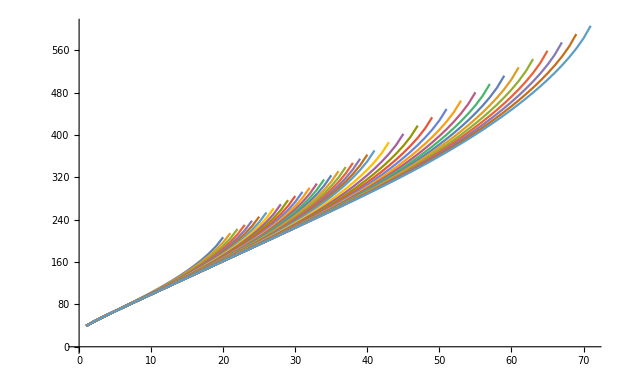

```mathematica
ListPlot[Table[rootsave[cent,tab⟦i⟧],{i,1,Length[tab]-20}], Joined->True]
```

```mathematica
(* differences between roots have also self-similarity pattern *)
```

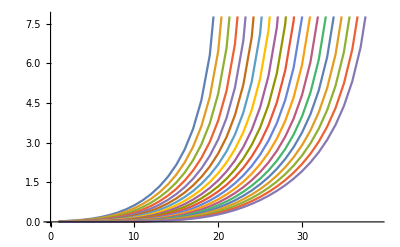

```mathematica
ListPlot[-Table[ rootsave[cent,tab⟦i+1⟧]⟦;;tab⟦i⟧/2⟧-rootsave[cent, tab⟦i⟧],{i,1,20}],Joined->True]
```

```mathematica
(*The answer for Subscript[Δ, 1] is exponentially converged when N~d. We have to increase the newton method stopping threshold to get accurate result when the result is pretty flat *)
```

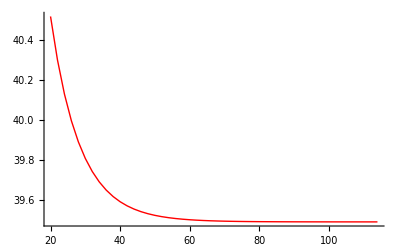

```mathematica
ListLinePlot[Join[ Table[{2i,2π*F[i][[1]]},{i,10,40}], Table[{tab[[i]],rootsave[cent,tab⟦i⟧]⟦1⟧},{i,23,30}]], PlotRange->All,PlotStyle-> {Red, Thick}]
```

```mathematica
data100= Join[ Table[{2i,2π*F[i][[1]]},{i,10,40}], Table[{tab[[i]],rootsave[cent,tab⟦i⟧]⟦1⟧},{i,23,30}]];
```

```mathematica
fitpol100= NonlinearModelFit[ data100,a+b/x+c1/x^2,{a,b,c1},x,WorkingPrecision->70,MaxIterations->1000];
```

```mathematica
fitexp100 =  NonlinearModelFit[ data100,a+ c1 Exp[-b x/100] ,{a,b,c1},x,WorkingPrecision->70,MaxIterations->1000];
```

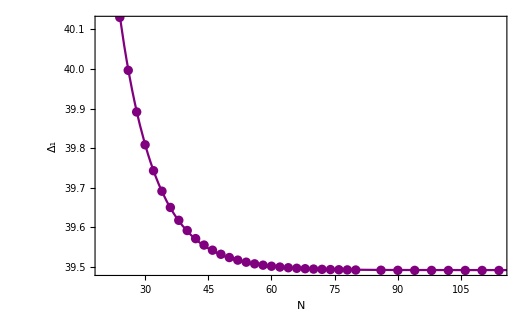

```mathematica
p1=ListPlot[data100(*,PlotLegends->Placed[PointLegend[{ Purple},{"Exponential Fit"}],{0.6,0.5}]*),PlotStyle->Purple];

p2=Plot[fitexp100[x],{x,0,2040}(*,PlotLegends->Placed[LineLegend[ {Purple},{""}],{0.6,0.4}]*),PlotStyle->Purple];

Show[{p1,p2},FrameLabel-> {Style["N",Black,FontSize->14],Style[ "Δ_1", Black,FontSize->14] },FrameStyle->Directive[Thick,Black,FontSize-> 10],BaseStyle->{FontWeight->  "Bold",FontSize-> 12},Frame-> True]
```

## Additional section : Results for d = 24, comparison for times for d = 24, High precision calculation of Leech lattice roots and coefficients, SDPB Solver code

d=24, corresponding to Leech Lattice, the lattice theta function corresponds to Klein’s J-function

```mathematica
(*This was done for virasoro case, the sphere packing bounds are the same in d=24 and d=8 which correspond to Subscript[E, 8] and Leech lattices ()
```

```mathematica
pre[x_]:=SetPrecision[x,25];
```

```mathematica
precise[x_]:=SetPrecision[x,1000];
```

```mathematica
<<"/home/ahttajdini/mx files/c12hans1000.mx"
```

```mathematica
c=12;
axx=coeff[-2π ((c-1)/12)//precise,hans[2000]];
```

```mathematica
(*the correct answer)
```

```mathematica
a1= 1728 KleinInvariantJ[Log[q]/(2π I)] -744;
a2= q^(-1/24)DedekindEta[Log[q]/(2π I)];
```

```mathematica
Series[ a2^2 a1,{q,0,23}]
```

1/q-2+196883 q+21099994 q^2+821115567 q^3+18496156326 q^4+291889812520 q^5+3567122650108 q^6+35861143437375 q^7+308613211961908 q^8+2337677474360082 q^9+15907213845000126 q^10+98756159287860025 q^11+566157642466093000 q^12+3026194949528518517 q^13+15200025410917722442 q^14+72208775347404813273 q^15+326202847038187290692 q^16+1407772709186898199750 q^17+5826834157376255048200 q^18+23209422534353220233823 q^19+89230568252431087159036 q^20+331977918214431847589875 q^21+1197975051416086685769000 q^22+4201603382114203552302533 q^23+O[q]^(277/12)

```mathematica
(*numerical answer for coefficients vs coefficients of Leech lattice theta function *)
```

```mathematica
Table[AccountingForm[axx[[i]],30],{i,1,23}]
```

{196882.000000000000000000000002,21099994.0000000000000000000004,821115567.000000000000000000034,18496156326.0000000000000000014,291889812520.000000000000000040,3567122650108.00000000000000084,35861143437375.0000000000000138,308613211961908.000000000000189,2337677474360082.00000000000223,15907213845000126.0000000000231,98756159287860025.0000000002147,566157642466093000.000000001813,3026194949528518517.00000001407,15200025410917722442.0000001014,72208775347404813273.0000006827,326202847038187290692.000004328,1407772709186898199750.00002596,5826834157376255048200.00014809,23209422534353220233823.0008064,89230568252431087159036.0042070,331977918214431847589875.021093,1197975051416086685769000.10192,4201603382114203552302533.47572}

```mathematica
(*the roots in Leech lattice are supposed to be integers. Below is the high precision result of optimization *)
```

```mathematica
SetPrecision[(hans[2000]/(2π)-1/12)⟦;;20⟧, 50]
```

{1.0000000000000000000000000000011975023946948192718,2.0000000000000000000000000000039235926268098647161,3.0000000000000000000000000000097957578659832233841,4.0000000000000000000000000000212599563638721030617,5.0000000000000000000000000000421498730994440358287,6.0000000000000000000000000000783358196846625607116,7.000000000000000000000000000138600188914580123267,8.0000000000000000000000000002358340897272762554117,9.0000000000000000000000000003886488118770287861145,10.000000000000000000000000000623530969592638794583,11.000000000000000000000000000977699510596404886778,12.000000000000000000000000001502866666632452164772,13.00000000000000000000000000227015497952274913643,14.000000000000000000000000003376486431598941264363,15.000000000000000000000000004952836647662318563808,16.000000000000000000000000007174841994177272986071,17.00000000000000000000000001027636246206441830166,18.000000000000000000000000014566743370490970452418,19.00000000000000000000000002045268857274938322816,20.000000000000000000000000028465863082304512951232}

Functional

```mathematica
(*from roots, we can reconstruct the functional, the functional has a single zero and for x>Subscript[Δ, 1], all roots are all double zeros  *)
```

```mathematica
F[5];
```

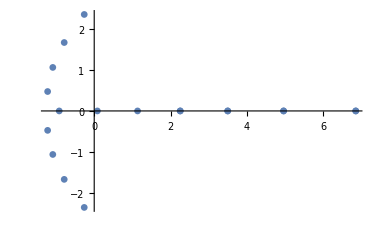

```mathematica
temp=(poly[2π F[5][[1;;5]]]//Expand)/.x->2π y//Expand;
zeros=y/.Solve[temp==0];
ListPlot[Transpose[{zeros//Re,zeros//Im}]]
```

```mathematica
F[5][[5]]//N
```

6.85237

```mathematica
s3=newtonMinimizer[lis];
```

N = 6; err= 9.864×10^-7; iters= 2; newton time =0.02034

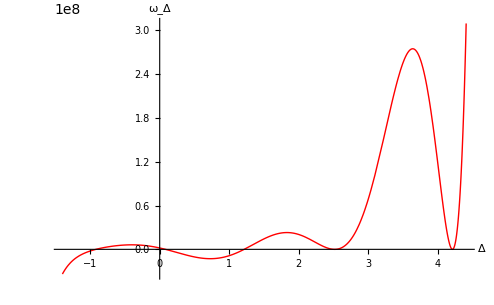

```mathematica
Plot[-poly[ s3[[1;;3]]]/.{x-> 2π y},{y,-1.4, 4.41},PlotRange-> All,WorkingPrecision->400,PlotStyle->{Red,Thick},AxesLabel->{Δ, Subscript[ω, Δ]},PlotTheme->"Classic" ]
```

Time comparison between SDPB and Us

```mathematica
(*Sample time difference between my fast algorithm and the traditional bounds using SDPB *)
```

```mathematica
<<"sdpbdatac12.mx"
```

```mathematica
<<"timefastalgorithmc12.mx"
```

```mathematica
(*for 2 CPU *)
```

```mathematica
time={{6,0.548033},{8,0.578904},{10,0.61834},{12,0.64514},{14,0.67824},{16,0.71853},{18,0.76759},{20,0.82513},{22,0.89151},{24,0.96792},{26,1.03964},{28,1.12080},{30,1.21243},{32,1.31573},{34,1.43250},{36,1.56371},{38,1.71059},{40,1.87258},{46,2.06919},{52,2.29123},{64,2.63478},{88,3.21847},{136,4.48781},{232,10.03205},{424,32.89041},{808,154.73286},{1576,1116.94094}};
```

```mathematica
tsdpb=  gaptime[[;;,{1,3}]];
```

```mathematica
cputsdpb= Table[{tsdpb[[i]] [[1]],2 tsdpb[[i]][[2]] } ,{i,1,Length[tsdpb]}];
```

```mathematica
sdpbfit= NonlinearModelFit[ cputsdpb, a x^b,{a,b},x,MaxIterations->200]
```

FittedModel[2.4581064×10^-8 x^5.6517188]

```mathematica
usfit= NonlinearModelFit[ time12⟦Length[time12]-6;; Length[time12] ⟧, a x^b,{a,b},x]
```

FittedModel[9.98223×10^-8 x^3.40096]

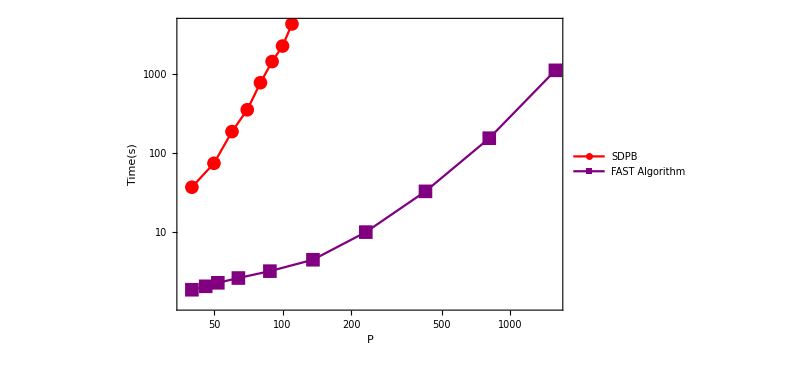

```mathematica
ex2=ListLogLogPlot[{ tsdpb, tus}, PlotStyle->{Red,Purple},GridLines->Automatic,FrameLabel-> {Style["P",Black,FontSize->14],Style[ "Time(s)", Black,FontSize->14] },FrameStyle->Directive[Black,FontSize-> 12],BaseStyle->{FontSize-> 12,FontFamily-> "Times"},PlotMarkers->{Automatic,14},Frame->True, RotateLabel->False,PlotLegends->Placed[PointLegend[{Red, Purple},{"SDPB","FAST Algorithm"},LegendFunction->"Frame", LegendMarkers->Automatic],{0.55,0.86}],Joined->{True,True}]
```

```mathematica
Export["/home/ahttajdini/Dropbox/fast-shared/timecomparison.eps", ex2, ImageSize-> 800]
```

/home/ahttajdini/Dropbox/fast-shared/timecomparison.eps

Semi - definite linear programming solver (SDPB).

```mathematica
(*This was the standard way of finding the bound. It uses SDPB which is solver for semi-definite linear programming. I first found the bounds using SDPB. Later on, we found a non-convex algorithm to do the calculation. It requires installation of SDPB written by David Simmons-Duffin. See https://github.com/davidsd/sdpb for more information*)
```

```mathematica
<<"/usr/share/doc/sdpb-doc/examples/mathematica/SDPB.m";
S=Simplify;

one=SetPrecision[1,1000];
Clear[P,Touchard];
Clear[α, objective, constraint , vars, norm];

myc = 12;
(*E1 = myc/12*KK;*)
```

```mathematica
α[EE_, N_?IntegerQ]:= Sum[LaguerreL[n,0, 2π *2EE]a[n], {n,1,N,2}]/.a[1]->1;
vars[N_] := objective[1,N]//Variables;
constraint[E1_,N_] := α[E1 + x, N];

vacpoly[i_,myc_]:=LaguerreL[i,0,2(-2π (myc-1)/12)]-2 ⅇ^(-2π)LaguerreL[i,0,2((-2π (myc-1)/12)+2π)]+ⅇ^(-4π)LaguerreL[i,0,2((-2π (myc-1)/12)+4π)];
objective[c_, N_] := Sum[vacpoly[n,c]a[n], {n,1,N,2}]/.a[1]->1;
```

```mathematica
prec=1000;
accura=10^-4;
gaptime={};
αlist={};
(*Print["------------- ",E1," --"];*)
```

```mathematica
tablist={{40,350},{50, 380},{60,460},{70, 500},{80,580}};
tablist4={{40,200},{50, 240},{60,250},{70, 260},{80,380}};
tablist2={{90,630},{100, 660}};
Print@Dynamic@n
Print@Dynamic@(SetPrecision[guessgap,10]);
Clear[i,k];
For[rr=5, rr≤ Length[Transpose[tablist4][[1]]], rr++,
n=tablist4[[rr,1]];
upper=SetPrecision[1.09,prec];
lower=SetPrecision[1.07,prec];
t0= AbsoluteTime[];
olist=DeleteCases[CoefficientList[objective[myc, n]/.a[i_]->Z^i,Z],0]one;
alist=DeleteCases[Table[If[CoefficientList[objective[myc, n]/.a[i_]->Z^i,Z]⟦k⟧≠0&&k≠1,a[k-1],0],{k,1,Length@CoefficientList[objective[myc, n]/.a[i_]->Z^i,Z]}],0];
norms={1}~Join~Table[0,{i,Length@olist-1}];
obj=olist;(*Table[0,{i,Length@olist}];*)


While[( upper-lower> accura)  ,
guessgap=1/2(upper+lower);
plist=DeleteCases[CoefficientList[constraint[guessgap, n]/.a[i_]->Z^i,Z],0]one;

pols={
PositiveMatrixWithPrefactor[
DampedRational[1,{},1/ⅇ,x],
{
{
plist
}
}
],
PositiveMatrixWithPrefactor[
DampedRational[1,{},1/ⅇ,x],
{
{
olist
}
}
]
};

sdpFile = "/home/ahttajdini/Desktop/mySDPdsa2"<>ToString[KhK]<>".xml";
outFile = "/home/ahttajdini/Desktop/mySDPdsa2"<>ToString[KhK]<>".out";
WriteBootstrapSDP[sdpFile,SDP[obj,norms,pols]];
(*Run["sdpb", "-s", sdpFile,
        "--stepLengthReduction=0.9 --noFinalCheckpoint --findPrimalFeasible --findDualFeasible --dualityGapThreshold=1e-140 --primalErrorThreshold=1e-140 --dualErrorThreshold=1e-140 --maxIterations=1000 --precision=2000 choleskyStabilizeThreshold=1e-40 "];*)
Run["sdpb", "-s", sdpFile,
        "--precision="<>ToString[tablist4[[rr,2]]],
"--maxThreads=2",
"--stepLengthReduction=0.7 --feasibleCenteringParameter=0.1  --infeasibleCenteringParameter=0.3 --initialMatrixScalePrimal=1e+20  --initialMatrixScaleDual=1e+20 --noFinalCheckpoint --findPrimalFeasible --findDualFeasible --dualityGapThreshold=1e-30 --primalErrorThreshold=1e-30 --dualErrorThreshold=1e-30 --maxIterations=1000  choleskyStabilizeThreshold=1e-40 "];
Get[outFile];
Clear[x];

test[1]=terminateReason;



If[(test[1]== "found primal feasible solution" ) ,lower= guessgap ];
If[test[1]=="found dual feasible solution",(upper=guessgap)];
If[test[1]== "maxComplementarity exceeded", Print["Numerical Instability"]; Break[]];
Pause[0.3];
];
αlist=AppendTo[αlist,{n,y}];
t1= AbsoluteTime[];
gaptime= AppendTo[gaptime,{n,guessgap,t1-t0}];

]
```

```mathematica
gaptime//N
```

{{40.,1.08992,43.8022},{50.,1.08805,129.3},{60.,1.08539,244.787},{70.,1.08461,443.186},{80.,1.08398,909.831},{40.,1.08992,31.9147},{50.,1.08805,72.4019},{60.,1.08539,191.971},{70.,1.08461,353.864},{80.,1.08398,763.683},{40.,1.08992,40.8021},{50.,1.08805,94.1067},{60.,1.08539,244.534},{70.,1.08461,444.83},{80.,1.08398,908.556},{40.,1.08992,41.0512},{50.,1.08805,93.0324},{60.,1.08539,257.275},{70.,1.08461,486.075},{80.,1.08398,1060.96},{40.,1.08992,26.2513},{50.,1.08992,69.4311},{60.,1.08992,183.081},{70.,1.08758,238.26},{80.,1.08523,501.459},{80.,1.08523,505.194}}

```mathematica
gapwith2core={{40.,1.0899218750000002,43.802239},{50.,1.088046875,129.300253},{60.,1.085390625,244.787389},{70.,1.084609375,443.186447},{80.,1.083984375,909.830873}}
```

```mathematica
DumpSave["sdpbdatac12.mx", {gaptime,αlist,tablist,tablist2}];
```

```mathematica
αlist//N//Dimensions
```

{8,2}

```mathematica
<<"sdpbdatac12.mx"
```

```mathematica
gg=gaptime[[;;,{1,3}]];
```

```mathematica
DumpSave["sdpbdatac12.mx", {gaptime,αlist,tablist}];
```

```mathematica
<<"timefastalgorithmc12.mx"
```

```mathematica
(*Comparison in time it takes for our algorithm and convex optimization using SDPB *)
```

```mathematica
ListLogLogPlot[{gg, time12}, GridLines->Automatic, PlotMarkers->Automatic,PlotLegends->Automatic]
```